# Cálculos Iniciais em LT aérea

## Antonio Carlos Siqueira de Lima 2022/1

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\anton\Dropbox\UFRJ\cursos\EEE457-Transmissão_Energia_Elétrica\arquivos_Mma_EEE457

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=100.0 ; (* comprimento do circuito *)
```

```mathematica
z=0.12160464662817234 + 0.48366929205670867 I;
y= 3.447800169070513*^-6 ⅈ;
Zc= Sqrt[z/y];
θ= Sqrt[ z y]ℓ;
```

```mathematica
Zc
```

377.447-46.722 ⅈ

```mathematica
Pn= (138)^2/ Zc
```

49.6933+6.15125 ⅈ

## Definição do quadripolo

```mathematica
Q={{Cosh[θ],Zc Sinh[θ]},{1/Zc Sinh[θ], Cosh[θ]}};
MatrixForm[Q]
```

(0.991673+0.00209052 ⅈ | 12.093+48.2411 ⅈ
-2.40524×10^-7+0.000343823 ⅈ | 0.991673+0.00209052 ⅈ)

```mathematica
Det[Q]
```

1.-5.55112×10^-17 ⅈ

```mathematica
Vr = 138. 10^3/Sqrt[3]
```

79674.3

## Definição da corrente no terminal receptor

```mathematica
P= 50. 10^6;
(* Ir= 50. 10^6/(Sqrt[3] 138 10^3)*)
```

```mathematica
Irr= Vr/Re[Zc]
```

211.087

```mathematica
Ir = Irr/ Cos[ 20 Degree]
```

224.634

```mathematica
Ir =1.25 Ir Exp[-I 20 Degree]
```

263.859-96.0369 ⅈ

```mathematica
Abs[Ir]
```

280.793

```mathematica
{Vs, Is}=Q.{Vr, Ir}
```

{86834.6+11734. ⅈ,261.844-67.2918 ⅈ}

## potência na carga e no emissor

```mathematica
Sr = 3Vr Conjugate[Ir]/10^6
```

63.0684+22.955 ⅈ

```mathematica
Ss= 3 10^-6Vs Conjugate[Is]
```

65.8425+26.7472 ⅈ

```mathematica
vs= Vs Sqrt[3]/138000.;
ib= 50 10^6/(Sqrt[3] 138000.);
is= Is/ib;
Abs[vs]
```

1.09978

```mathematica
Abs[is]
```

1.29241

```mathematica
Arg[vs]/π 180
```

7.69582

```mathematica
Arg[Is]/π 180
```

-14.4127

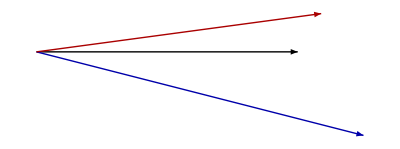

```mathematica
Graphics[{Arrow[{{0,0}, {1,0}}],{Darker@Blue, Arrow[{{0,0},{ Re[is], Im[is]}}]}, {Darker@ Red, Arrow[{{0,0}, {Re[vs], Im[vs]}}]}}]
```